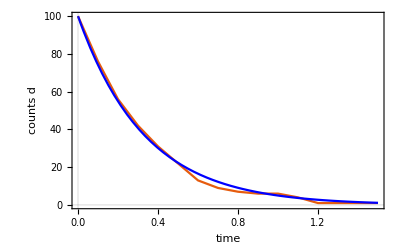
-Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]];
countsA=Import["data/A.txt","Table"];

leg=LineLegend[{Red,Blue},{"Gillespie","Theory"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];

plt=Grid[{{
Show[
ListLinePlot[countsA,FrameLabel->{"time","counts"d},PlotStyle->Re],
Plot[countsA[[1,2]]*Exp[-3*t],{t,0,countsA[[-1,1]]},PlotStyle->Blue,PlotRange->All]
],
leg}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figure.jpg",plt,ImageResolution->200]
```

figure.jpg